# Practical 5 Solution of system of ODE

Solve the system of ODE

y1’=-3y1+y2
y2’=y1-3y2

Clear[sol, eq1, eq2, y, x, t]

```mathematica
eq1=y'[t]==-3y[t]+x[t]
eq2=x'[t]==y[t]-3x[t]
```

y'[t]==x[t]-3 y[t]

x'[t]==-3 x[t]+y[t]

```mathematica
sol=DSolve[{eq1,eq2},{y[t],x[t]},t]
```

{{x[t]→1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)) C[1]+1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)) C[2],y[t]→1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)) C[2]}}

```mathematica
sol[[1,1]]
sol[[1,2]]
```

x[t]→1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)) C[1]+1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)) C[2]

y[t]→1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)) C[2]

```mathematica
tab=Table[{x[t]/.sol[[1,1]],y[t]/.sol[[1,2]]}/.{C[1]->i,C[2]->j},
{i,-1,0},{j,0,1}]//Flatten
```

{-1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)),1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))-1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),-1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t))+1/2 ⅇ^(-4 t) (1+ⅇ^(2 t)),0,0,1/2 ⅇ^(-4 t) (-1+ⅇ^(2 t)),1/2 ⅇ^(-4 t) (1+ⅇ^(2 t))}

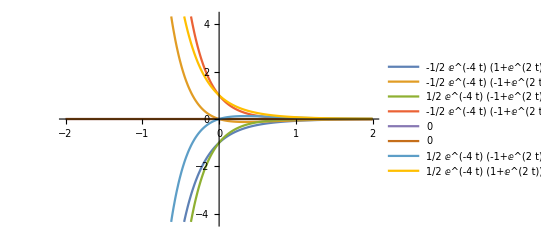

```mathematica
Plot[Evaluate[tab],{t,-2,2},PlotLegends->"Expressions"]
```

y1’=-5y1+2y2
y2’=2y1-2y2,y1(0)=1,y2(0)=-2

Clear[x, y, t, eq1, eq2, sol]

```mathematica
eq1=x'[t]==-5x[t]+2y[t]
eq2=y'[t]==2x[t]-2y[t]
```

x'[t]==-5 x[t]+2 y[t]

y'[t]==2 x[t]-2 y[t]

```mathematica
sol=DSolve[{eq1,eq2,x[0]==1,y[0]==-2},{x[t],y[t]},t]
```

{{x[t]→-1/5 ⅇ^(-6 t) (-8+3 ⅇ^(5 t)),y[t]→-2/5 ⅇ^(-6 t) (2+3 ⅇ^(5 t))}}

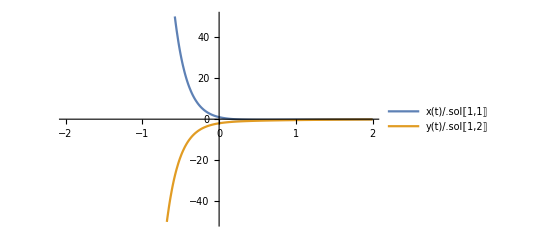

```mathematica
Plot[{x[t]/.sol[[1,1]],y[t]/.sol[[1,2]]},{t,-2,2},PlotRange->{-50,50},PlotLegends->"Expressions"]
```

*Alternative Method

y1’=-3y1+y2
y2’=y1-3y2

```mathematica
matrixa={{-3,1},{1,-3}}
polya=CharacteristicPolynomial[matrixa,lambda]
```

{{-3,1},{1,-3}}

8+6 lambda+lambda^2

```mathematica
eigs=Solve[polya==0,lambda](*Distinct and real*)
```

{{lambda→-4},{lambda→-2}}

```mathematica
system1=(matrixa-(lambda/.eign[[1]])IdentityMatrix[2]).{y1,y2}
```

{y1+y2,y1+y2}

```mathematica
system2=(matrixa-(lambda/.eign[[2]])IdentityMatrix[2]).{x1,x2}
```

{-x1+x2,x1-x2}

```mathematica
Solve[system1==0,y2]
```

{{y2→-y1}}

```mathematica
Solve[system2==0,x2]
```

{{x2→x1}}

```mathematica
X1={1,-1};
X2={1,1};
```

```mathematica
sol=c1 X1 E^(eigs[[1,1]]x)+c2 X2 E^(eigs[[1,2]]x)(*general sol*)
```

{c1 ⅇ^(-4 x)+c2 ⅇ^(-2 x),-c1 ⅇ^(-4 x)+c2 ⅇ^(-2 x)}

Alternative(using Eigensystem)

```mathematica
matrix={{-3,1},{1,-3}}
```

{{-3,1},{1,-3}}

```mathematica
matrix//MatrixForm
```

(-3 | 1
1 | -3)

```mathematica
eigs=Eigensystem[matrix]
(*-4 is an eigenvalueof the matrix extracted with eigs from eigs[[1,1]] & {-1,1} is corresponding eigenvector extracted with eigs from eign[[2,1]],
similarly for eigenvalue -2*)(*Distinct and real *)
```

{{-4,-2},{{-1,1},{1,1}}}

```mathematica
eigs[[1,1]]
```

-4

```mathematica
eigs[[1,2]]
```

-2

```mathematica
(matrix-eigs[[1,1]]IdentityMatrix[2]).eigs[[2,1]]//Simplify
```

{0,0}

```mathematica
(matrix-eigs[[1,2]]IdentityMatrix[2]).eigs[[2,2]]//Simplify
```

{0,0}

```mathematica
sol=c1 eigs[[2,1]]E^(eigs[[1]]x)+c2 eigs[[2,2]]E^(eigs[[1,2]]x)(*general sol*)
```

{-c1 ⅇ^(-4 x)+c2 ⅇ^(-2 x),c1 ⅇ^(-2 x)+c2 ⅇ^(-2 x)}

y1’=5y1+3y2
y2’=4y1+y2

```mathematica
Clear[sol,eq1,eq2,y,x,t]
eq1=x'[t]==5x[t]+3y[t]
eq2=y'[t]==4x[t]+y[t]
```

x'[t]==5 x[t]+3 y[t]

y'[t]==4 x[t]+y[t]

```mathematica
sol=DSolve[{eq1,eq2},{x[t],y[t]},t]
```

{{x[t]→1/4 ⅇ^-t (1+3 ⅇ^(8 t)) C[1]+3/8 ⅇ^-t (-1+ⅇ^(8 t)) C[2],y[t]→1/2 ⅇ^-t (-1+ⅇ^(8 t)) C[1]+1/4 ⅇ^-t (3+ⅇ^(8 t)) C[2]}}

```mathematica
sol[[1,1]]
```

x[t]→1/4 ⅇ^-t (1+3 ⅇ^(8 t)) C[1]+3/8 ⅇ^-t (-1+ⅇ^(8 t)) C[2]

```mathematica
sol[[1,2]]
```

y[t]→1/2 ⅇ^-t (-1+ⅇ^(8 t)) C[1]+1/4 ⅇ^-t (3+ⅇ^(8 t)) C[2]

```mathematica
tab=Table[{x[t]/.sol[[1,1]],y[t]/.sol[[1,2]]}/.{C[1]->i,C[2]->j},{i,-1,0},{j,0,1}]//Flatten
```

{-1/4 ⅇ^-t (1+3 ⅇ^(8 t)),-1/2 ⅇ^-t (-1+ⅇ^(8 t)),3/8 ⅇ^-t (-1+ⅇ^(8 t))-1/4 ⅇ^-t (1+3 ⅇ^(8 t)),-1/2 ⅇ^-t (-1+ⅇ^(8 t))+1/4 ⅇ^-t (3+ⅇ^(8 t)),0,0,3/8 ⅇ^-t (-1+ⅇ^(8 t)),1/4 ⅇ^-t (3+ⅇ^(8 t))}

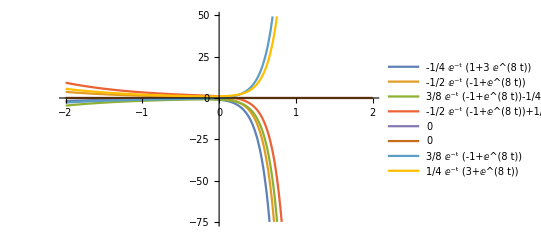

```mathematica
Plot[Evaluate[tab],{t,-2,2},PlotLegends->"Expressions"]
```

y1’=3y1+5y2
y2’=-2y1+5y2 , x(0)=5,y(0)=-1

```mathematica
Clear[x,y,t,eq1,eq2,sol]
```

```mathematica
eq1=x'[t]==3x[t]+5y[t]
eq2=y'[t]==-2x[t]+5y[t]
```

x'[t]==3 x[t]+5 y[t]

y'[t]==-2 x[t]+5 y[t]

```mathematica
sol=DSolve[{eq1,eq2,x[0]==5,y[0]==-1},{x[t],y[t]},t]
```

{{x[t]→5/3 ⅇ^(4 t) (3 Cos[3 t]-2 Sin[3 t]),y[t]→-1/3 ⅇ^(4 t) (3 Cos[3 t]+11 Sin[3 t])}}

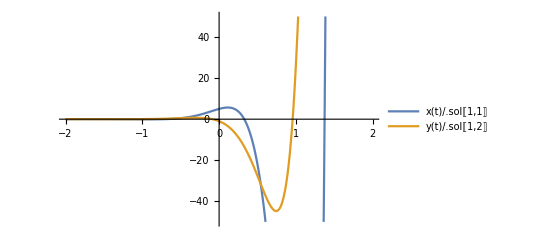

```mathematica
Plot[{x[t]/.sol[[1,1]],y[t]/.sol[[1,2]]},{t,-2,2},PlotRange->{-50,50},PlotLegends->"Expressions"]
```

y1’=7y1+4y2
y2’=-1y1+3y2

```mathematica
Clear[sol,eq1,eq2,y,x,t]
```

```mathematica
eq1=x'[t]==7x[t]+4y[t]
eq2=y'[t]==-x[t]+3y[t]
```

x'[t]==7 x[t]+4 y[t]

y'[t]==-x[t]+3 y[t]

```mathematica
sol=DSolve[{eq1,eq2},{x[t],y[t]},t]
```

{{x[t]→ⅇ^(5 t) (1+2 t) C[1]+4 ⅇ^(5 t) t C[2],y[t]→-ⅇ^(5 t) t C[1]-ⅇ^(5 t) (-1+2 t) C[2]}}

```mathematica
sol[[1,1]]
```

x[t]→ⅇ^(5 t) (1+2 t) C[1]+4 ⅇ^(5 t) t C[2]

```mathematica
sol[[1,2]]
```

y[t]→-ⅇ^(5 t) t C[1]-ⅇ^(5 t) (-1+2 t) C[2]

```mathematica
tab2=Table[{x[t]/.sol[[1,1]],y[t]/.sol[[1,2]]/.C[1]->i,C[2]->j},{i,-1,0},{j,0,1}]//Flatten
```

{ⅇ^(5 t) (1+2 t) C[1]+4 ⅇ^(5 t) t C[2],ⅇ^(5 t) t-ⅇ^(5 t) (-1+2 t) C[2],C[2]→0,ⅇ^(5 t) (1+2 t) C[1]+4 ⅇ^(5 t) t C[2],ⅇ^(5 t) t-ⅇ^(5 t) (-1+2 t) C[2],C[2]→1,ⅇ^(5 t) (1+2 t) C[1]+4 ⅇ^(5 t) t C[2],-ⅇ^(5 t) (-1+2 t) C[2],C[2]→0,ⅇ^(5 t) (1+2 t) C[1]+4 ⅇ^(5 t) t C[2],-ⅇ^(5 t) (-1+2 t) C[2],C[2]→1}

```mathematica
Plot[Evaluate[tab2],{t,-2,2},PlotLegends->"Expressions"]
```

-Graphics-